```mathematica
Simplify[Integrate[z Exp[-z^2+2 I π/h z], {z,-Infinity,Infinity}],Assumptions->{y>0}]
```

(ⅈ ⅇ^(-π^2/h^2) π^(3/2))/h

```mathematica
Integrate[x Exp[-x^2],{x,0,Infinity}]
```

1/2

```mathematica
Plot[ⅇ^(y^2) √π HypergeometricU[-1/2,0,y^2],{y,-10.392304845413262,10.392304845413262}]
```

-Graphics-

```mathematica
Simplify[Abs[ComplexExpand[Exp[-(x+I y)^2]]], Assumptions->{x>0,y>0}]
```

ⅇ^(-x^2+y^2) Abs[Cos[2 x y]-ⅈ Sin[2 x y]]

```mathematica
Simplify[1/z Integrate[Exp[-π^2/h^2 z^2/(4 σ^2)+I π/h z],{z,-Infinity,Infinity}],Assumptions->{σ>0,h>0}]
```

(2 ⅇ^(-σ^2) h σ)/(√π z)

```mathematica
Integrate[Exp[- (R+I y)^2/(4 σ^2)-I (R+I y)]]
```

```mathematica
Simplify[Abs[ComplexExpand[Exp[- (R/h+I y)^2/(4 σ^2)-3I (R/h+I y)]]], Assumptions->{R>0,σ>0,y>0,h>0}]
```

ⅇ^(3 y-R^2/(4 h^2 σ^2)+y^2/(4 σ^2)) Abs[Cos[(R (y+6 σ^2))/(2 h σ^2)]-ⅈ Sin[(R (y+6 σ^2))/(2 h σ^2)]]

```mathematica
Integrate[Exp[-x^2/(4 σ^2)] x^(1/2)BesselJ[-1/2,x],{x,0,Infinity}, Assumptions->{σ>0}]
```

√2 ⅇ^(-σ^2) σ

```mathematica
(1/Sqrt[2 π](Integrate[ⅇ^(-(R^2-y^2+4 y σ^2)/(4 σ^2)),{y,0,π^2/(2 h)}, Assumptions->{R>0,σ>0}]+Integrate[ⅇ^(-(R^2-y^2+12 y σ^2)/(4 σ^2)),{y,0,π^2/(2 h)}, Assumptions->{R>0,σ>0}]+
Integrate[ⅇ^((-R^2+y (y+4 σ^2))/(4 σ^2)),{y,-π^2/(2 h),0}, Assumptions->{R>0,σ>0}]+Integrate[ⅇ^((-R^2+y (y+12 σ^2))/(4 σ^2)),{y,-π^2/(2 h),0}, Assumptions->{R>0,σ>0}]+Integrate[x^□])/(√2 ⅇ^(-σ^2) σ))//Expand//Simplify
```

(ⅇ^(σ^2) Integrate)/(2 √π σ)+ⅇ^(-R^2/(4 σ^2)-8 σ^2) Erfi[π^2/(4 h σ)-3 σ]+ⅇ^(-R^2/(4 σ^2)) Erfi[π^2/(4 h σ)-σ]+ⅇ^(-R^2/(4 σ^2)) Erfi[σ]+ⅇ^(-R^2/(4 σ^2)-8 σ^2) Erfi[3 σ]

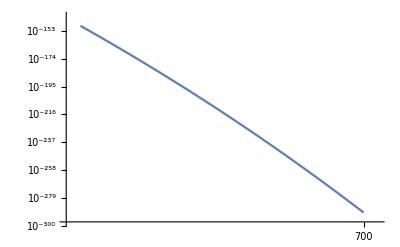

```mathematica
LogLogPlot[Abs[%653/. R-> h n/.h-> 0.1/.σ-> 1], {n,600,700}]
```

```mathematica
FullSimplify[2 ⅇ^(-(R^2+4 σ^4)/(4 σ^2)) √π σ (Erfi[π^2/(4 h σ)-σ]+Erfi[σ])+2 ⅇ^(-R^2/(4 σ^2)-9 σ^2) √π σ (Erfi[π^2/(4 h σ)-3 σ]+Erfi[3 σ]), Assumptions->{σ>0,R>0,h>0}]
```

2 ⅇ^(-R^2/(4 σ^2)-9 σ^2) √π σ (Erfi[π^2/(4 h σ)-3 σ]+ⅇ^(8 σ^2) (Erfi[π^2/(4 h σ)-σ]+Erfi[σ])+Erfi[3 σ])